Utilización promedio de los servidores: 49.9301%

Tasa media de llegadas: 0.0553984 clientes/minuto

Tasa media de servicios: 9.0195 minutos/cliente

Nro. promedio en el tiempo de clientes en cola: 0.486376 clientes

Valor analítico - fórmula: 0.5 clientes

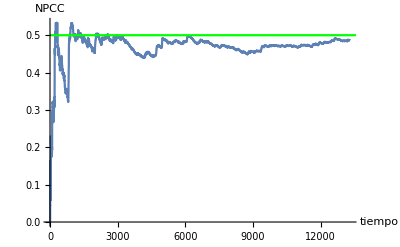

Demora promedio por cliente en cola: 8.78367 minutos

Valor analítico - fórmula: 9. minutos

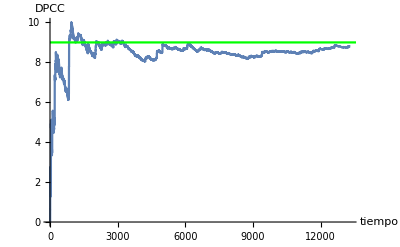

Tiempo promedio de clientes en sistema: 17.8032 minutos

Valor analítico - fórmula: 18. clientes

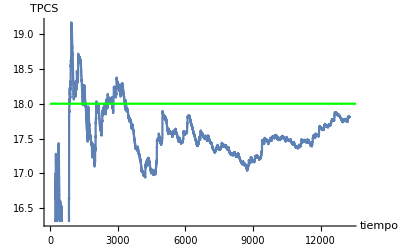

Nro. promedio en el tiempo de clientes en sistema: 0.985676 clientes

Valor analítico - fórmula: 1. clientes

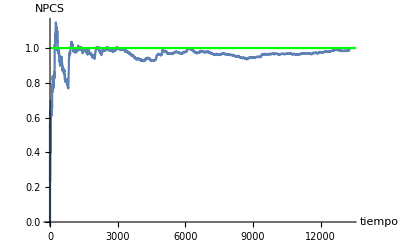

Area bajo la curva del subintervalo - 1: 3496.8 - Media del subintervalo: 0.885266

Area bajo la curva del subintervalo - 2: 4641.17 - Media del subintervalo: 1.17498

Area bajo la curva del subintervalo - 3: 3619.21 - Media del subintervalo: 0.916255

Area bajo la curva del subintervalo - 4: 3483.75 - Media del subintervalo: 0.881961

Area bajo la curva del subintervalo - 5: 4338.63 - Media del subintervalo: 1.09839

Area bajo la curva del subintervalo - 6: 3943.04 - Media del subintervalo: 0.998237

Area bajo la curva del subintervalo - 7: 4268.48 - Media del subintervalo: 1.08063

Area bajo la curva del subintervalo - 8: 2831.8 - Media del subintervalo: 0.71691

Area bajo la curva del subintervalo - 9: 2624.81 - Media del subintervalo: 0.664509

Area bajo la curva del subintervalo - 10: 3548.18 - Media del subintervalo: 0.898273

Area bajo la curva del subintervalo - 11: 5125.19 - Media del subintervalo: 1.29752

Area bajo la curva del subintervalo - 12: 4131.89 - Media del subintervalo: 1.04605

Area bajo la curva del subintervalo - 13: 3914.43 - Media del subintervalo: 0.990994

Area bajo la curva del subintervalo - 14: 4603.92 - Media del subintervalo: 1.16555

Area bajo la curva del subintervalo - 15: 3563.33 - Media del subintervalo: 0.90211

Area bajo la curva del subintervalo - 16: 3112. - Media del subintervalo: 0.787849

Area bajo la curva del subintervalo - 17: 3862.95 - Media del subintervalo: 0.977961

Area bajo la curva del subintervalo - 18: 3241.04 - Media del subintervalo: 0.820516

Area bajo la curva del subintervalo - 19: 2806.46 - Media del subintervalo: 0.710496

Area bajo la curva del subintervalo - 20: 3480.45 - Media del subintervalo: 0.881126

Area bajo la curva del subintervalo - 21: 4350.2 - Media del subintervalo: 1.10132

Area bajo la curva del subintervalo - 22: 5175.61 - Media del subintervalo: 1.31028

Area bajo la curva del subintervalo - 23: 3489.25 - Media del subintervalo: 0.883354

Area bajo la curva del subintervalo - 24: 4336.56 - Media del subintervalo: 1.09786

Area bajo la curva del subintervalo - 25: 3835.51 - Media del subintervalo: 0.971015

Area bajo la curva del subintervalo - 26: 3544.41 - Media del subintervalo: 0.897318

Area bajo la curva del subintervalo - 27: 5031.86 - Media del subintervalo: 1.27389

Area bajo la curva del subintervalo - 28: 4207.55 - Media del subintervalo: 1.0652

Area bajo la curva del subintervalo - 29: 4649.82 - Media del subintervalo: 1.17717

Area bajo la curva del subintervalo - 30: 3787.4 - Media del subintervalo: 0.958837

Media muestral: 0.987727

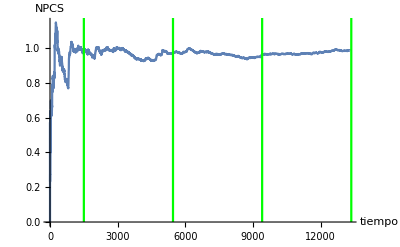

Probabilidad de que haya un cliente en Sistema 0.250058

Valor analítico - fórmula: 0.25

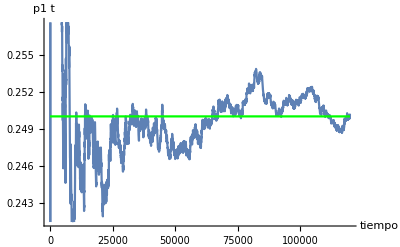

```mathematica
Quit;
ClearAll;
(***** DEFINICION DE FUNCIONES *****)
(* Rutina de tiempos *)
tiempos[] := Module[{menor, eme},
menor = Position[listaDeEventos, Min[listaDeEventos]];
eme = First[First[menor]];
tiempoUltimoEvento = reloj;
reloj = listaDeEventos[[eme]];
proximoEvento = tiposEventos[[eme]];
];

(* Rutina de arribos *)
arribos[] := Module[{tarr},
tarr = RandomVariate[ExponentialDistribution[1/tmEntreArribos]];
listaDeEventos[[1]]=reloj+tarr;
If[estadoServidor=="D",
estadoServidor="O";
tserv = RandomVariate[ExponentialDistribution[1/tmDeServicio]];
listaDeEventos = ReplacePart[listaDeEventos, 2->(reloj + tserv)];
tsAcumuladoUlt = tsAcumulado;(* 20170701 - Corrección del % de utilización del servidor *)
tsAcumulado = tsAcumulado + tserv;
completaronDemora = completaronDemora + 1;
,(* Else *)
areaQDeT = areaQDeT + (nroDeClientesEnCola * (reloj - tiempoUltimoEvento));
nroDeClientesEnCola = nroDeClientesEnCola + 1;
cola = Prepend[cola, reloj];
];
];

(* Rutina de partidas *)
partidas[] := Module[{tserv, tdem},
If[nroDeClientesEnCola > 0,
tserv = RandomVariate[ExponentialDistribution[1/tmDeServicio]];
listaDeEventos = ReplacePart[listaDeEventos, 2-> (reloj + tserv)];
tdem = reloj - cola[[1]];
demoraAcumulada = demoraAcumulada + tdem;
completaronDemora = completaronDemora + 1;
tsAcumuladoUlt = tsAcumulado;(* 20170701 - Corrección del % de utilización del servidor *)
tsAcumulado = tsAcumulado + tserv;
areaQDeT = areaQDeT + (nroDeClientesEnCola*(reloj-tiempoUltimoEvento));
nroDeClientesEnCola = nroDeClientesEnCola - 1;
cola = Delete[cola,1],(* Else *)
estadoServidor = "D"; 
listaDeEventos = ReplacePart[listaDeEventos, 2 -> 999999];
];
];

(* Cálculo de variables de respuesta *)
calculaVR[] := Module[{},
nroPromCliCola = areaQDeT/reloj;
nroPromCliSis = areaSDeT/reloj;(* 20170827 - Gráfico nro. promedio de clientes en el sistema *)
demPromPorCli = demoraAcumulada/completaronDemora;
demPromPorCliSis = (demoraAcumulada + tsAcumulado)/completaronDemora; (* 20170827 - Gráfico tiempo promedio de clientes en el sistema *)
(* utilizServ=tsAcumulado/reloj; 20170701 - Corrección del % de utilización del servidor *)
utilizServ=tsAcumuladoUlt/reloj;(* 20170701 - Corrección del % de utilización del servidor *)
];

(* Definición e inicialización de variables *)
reloj = 0;
estadoServidor="D";
proximoEvento="null";
tiposEventos = {"Arribo","Partida"};
listaDeEventos = {};
cola={};
tsAcumulado = 0.0;
tsAcumuladoUlt = 0.0;(* 20170701 - Corrección del % de utilización del servidor *)
demoraAcumulada = 0.0;
nroDeClientesEnCola = 0;
areaQDeT = 0.0;
areaSDeT = 0.0;(* 20170827 - Gráfico nro. promedio de clientes en el sistema *)
nroCCUlt = 0;(* 20170827 - Gráfico nro. promedio de clientes en el sistema *)
tiempoUltimoEvento = 0.0;
completaronDemora = 0;
tmEntreArribos = 18.0;(* 1/λ *)
tmDeServicio = 9.0;(* 1/μ *)
tmax = 2000*60; (* 2000 horas - 120000 minutos *)
tasaLlegadas = 0.0; (* 20170618 *)
tasaServicios = 0.0; (* 20170618 *)
factorUtilizacion = 0.0; (* 20170618 *)
probClientes = 0.0; (* 20170618 *)
vRespuesta={};
areaSDeTNue = {}; (* 20170827 - Gráfico método de subintervalos *)
listaDeEventos=Append[listaDeEventos,RandomVariate[ExponentialDistribution[1/tmEntreArribos]]];
listaDeEventos=Append[listaDeEventos,999999];
tabla=Table[{"Reloj", "Tipo_Ev", "t_Arribos","t_Partidas","estado_serv","nro_CC", "nro_CCD", "area_Qt", "ts_acum", "dem_Acum", "area_St"},1]; (* 20170827 - Gráfico nro. promedio de clientes en el sistema *)
tabla=Append[tabla, {reloj, proximoEvento, listaDeEventos[[1]],listaDeEventos[[2]],estadoServidor, nroDeClientesEnCola,completaronDemora, areaQDeT, tsAcumulado,demoraAcumulada,areaSDeT}];(* 20170827 - Gráfico nro. promedio de clientes en el sistema *)
vRespuesta = Table[{"Reloj", "Nro_PTCC", "Dem_PPC", "Uti_PS", "Nro_PTCS", "Dem_PPCS"},1]; (* 20170827 - Gráficos nro. y tiempo promedio de clientes en el sistema *)

(* Programa principal *)
While[reloj≤tmax,
a=tiempos[];
If[proximoEvento=="Arribo",
a=arribos[];
,
a=partidas[];
];

(* 20170827 - INICIO Gráfico nro. promedio de clientes en el sistema *)
(* If - 1 *)
If[(estadoServidor=="D"||nroDeClientesEnCola>0||nroCCUlt>0)&& reloj>0, 
(* If - 2 *)
If[nroDeClientesEnCola>0,
(* If - 3 *)
If[proximoEvento=="Partida",areaSDeT = areaSDeT + ((reloj-tiempoUltimoEvento)*(nroCCUlt+1)),(* Else - 3 *)
areaSDeT = areaSDeT + ((reloj-tiempoUltimoEvento)*nroDeClientesEnCola)];nroCCUlt = nroDeClientesEnCola;,(* Else - 2 *)
areaSDeT = areaSDeT + ((reloj-tiempoUltimoEvento)*(nroCCUlt+1));nroCCUlt = 0;],(* Else - 1 *)
nroCCUlt = 0;
];
(* 20170827 - FIN Gráfico nro. promedio de clientes en el sistema *)

tabla=Append[tabla,{reloj,proximoEvento,listaDeEventos[[1]],listaDeEventos[[2]],estadoServidor,nroDeClientesEnCola,completaronDemora,areaQDeT,tsAcumulado,demoraAcumulada, areaSDeT}]; (* 20170827 - Gráfico nro. promedio de clientes en el sistema *)
a=calculaVR[];
vRespuesta=Append[vRespuesta,{reloj,nroPromCliCola,demPromPorCli,utilizServ,nroPromCliSis,demPromPorCliSis}];(* 20170827 - Gráficos nro. y tiempo promedio de clientes en el sistema *)
];

nroPromCliCola=areaQDeT/reloj;
nroPromCliSis=areaSDeT/reloj; (* 20170827 - Gráfico nro. promedio de clientes en el sistema *)
demPromPorCli=demoraAcumulada/completaronDemora;
demPromPorCliSis = (demoraAcumulada+tsAcumulado)/completaronDemora; (* 20170827 - Gráfico tiempo promedio de clientes en el sistema *)
(*utilizServ=tsAcumulado/reloj; 20170701 - Corrección del % de utilización del servidor *)
utilizServ=tsAcumuladoUlt/reloj;(* 20170701 - Corrección del % de utilización del servidor *)
tasaLlegadas =completaronDemora/tiempoUltimoEvento; (* 20170618 *)
tasaServicios = tsAcumulado/completaronDemora; (* 20170618 *)
factorUtilizacion = tmEntreArribos^(-1)/tmDeServicio^(-1); (* λ/μ - 20170618 *)
probClientes =(1-factorUtilizacion)*(factorUtilizacion)^3; (* (1-(λ/μ)).(λ/μ)3 - 20170618 *)

(* Reporte *)
Print["Utilización promedio de los servidores: ",utilizServ*100,"%"]
Print["Tasa media de llegadas: ",tasaLlegadas," clientes/minuto"] (* 20170618 *)
Print["Tasa media de servicios: ",tasaServicios," minutos/cliente\n"] (* 20170618 *)
(* Print["Probabilidad de exactamente 3 elementos en el sistema: ",probClientes*100,"%"] *)

Grid[tabla];
Grid[vRespuesta];

(* Gráficos *)
(* Gráfico 1 - Nro. promedio en el tiempo de clientes en cola *)
(* Creamos una tabla sólo con el nro. promedio de clientes en cola *)
nroPCCt = vRespuesta[[All,2]];
nroPCCt = Delete[nroPCCt,1];
Grid[nroPCCt];
g1 = ListLinePlot[nroPCCt, AxesLabel->{tiempo,NPCC}];
nroPCCm = (factorUtilizacion)^2*(1-factorUtilizacion)^(-1); (* valor analítico - fórmula *)
solana1 = Plot[nroPCCm,{x,0,tiempoUltimoEvento},PlotStyle->Green];
Print["Nro. promedio en el tiempo de clientes en cola: ",nroPromCliCola," clientes"];
Print["Valor analítico - fórmula: ",nroPCCm," clientes"];
Show[g1,solana1]

(* Gráfico 2 - Demora promedio por cliente en cola *)
(* Creamos una tabla sólo con la demora promedio de clientes en cola *)
demPCCt = vRespuesta[[All,3]];
demPCCt = Delete[demPCCt,1];
Grid[demPCCt];
g2 = ListLinePlot[demPCCt, AxesLabel->{tiempo,DPCC}];
demPCCm = (tmEntreArribos^(-1)/tmDeServicio^(-2))*(1-factorUtilizacion)^(-1); (* valor analítico - fórmula *)
solana2 = Plot[demPCCm,{x,0,tiempoUltimoEvento},PlotStyle->Green];
Print["\nDemora promedio por cliente en cola: ",demPromPorCli, " minutos"];
Print["Valor analítico - fórmula: ",demPCCm," minutos"];
Show[g2,solana2]

(* 20170827 - Gráfico 3 - Tiempo promedio de clientes en sistema *)
(* Creamos una tabla sólo con el tiempo promedio de clientes en sistema *)
tiePCSt = vRespuesta[[All,6]];
tiePCSt = Delete[tiePCSt,1];
Grid[tiePCSt];
g3 = ListLinePlot[tiePCSt, AxesLabel->{tiempo,TPCS}];
tiePCSm = tmDeServicio*(1-factorUtilizacion)^(-1); (* valor analítico - fórmula *)
solana3 = Plot[tiePCSm,{x,0,tiempoUltimoEvento},PlotStyle->Green];
Print["\nTiempo promedio de clientes en sistema: ",demPromPorCliSis," minutos"];
Print["Valor analítico - fórmula: ",tiePCSm," clientes"];
Show[g3,solana3]

(* 20170827 - Gráfico 4 - Nro. promedio en el tiempo de clientes en sistema *)
(* Creamos una tabla sólo con el nro. promedio de clientes en sistema *)
nroPCSt = vRespuesta[[All,5]];
nroPCSt = Delete[nroPCSt,1];
Grid[nroPCSt];
g4 = ListLinePlot[nroPCSt, AxesLabel->{tiempo,NPCS},PlotRange->All];
nroPCSm = factorUtilizacion*((1-factorUtilizacion)^(-1)); (* valor analítico - fórmula *)
solana4 = Plot[nroPCSm,{x,0,tiempoUltimoEvento},PlotStyle->Green];
Print["\nNro. promedio en el tiempo de clientes en sistema: ",nroPromCliSis," clientes"];
Print["Valor analítico - fórmula: ",nroPCSm," clientes"];
Show[g4,solana4]

(* 20170827 - Gráfico 5 - Método de subintervalos *)
lonPerTra = 1500; (* Longitud en minutos del período transitorio *)
(* lonPerTra = 80;  Prueba *)
lonSubInt = 3950; (* Longitud en minutos de cada subintervalo *)
(* lonSubInt = 25;  Prueba *)
canSubInt = Round[(tmax-lonPerTra)/lonSubInt];(* cantidad de subintervalos *)
subInt = tabla[[All,{1,11}]];
subInt = Delete[subInt,1];
solana5 = ParametricPlot[{{lonPerTra,t},{lonPerTra+lonSubInt,t},{lonPerTra+2*lonSubInt,t},{lonPerTra+3*lonSubInt,t},{lonPerTra+4*lonSubInt,t},{lonPerTra+5*lonSubInt,t},{lonPerTra+6*lonSubInt,t},{lonPerTra+7*lonSubInt,t},{lonPerTra+8*lonSubInt,t},{lonPerTra+9*lonSubInt,t},{lonPerTra+10*lonSubInt,t}},{t,0,tiempoUltimoEvento},PlotStyle->Green];
Grid[subInt];
medMue = 0.0;
tieLim = lonPerTra+lonSubInt;
(* PPrint["1 - tieLim: ", tieLim]; *)
i=1;
While [subInt[[i,1]]<lonPerTra,areaSDeTAnt= subInt[[i,2]];i++] (* quitamos el período inicial *)
(* Print["1 - areaSDeTAnt: ", areaSDeTAnt]; *)

For[j=1,j<=canSubInt,j++,
tieLim = lonPerTra+(j*lonSubInt);
While[subInt[[i,1]]<tieLim,areaSDeTNue = Append[areaSDeTNue,subInt[[i,2]]];i++] ;
medMue = medMue + ((Last[areaSDeTNue]-areaSDeTAnt)/lonSubInt)/canSubInt;
Print["Area bajo la curva del subintervalo - ",j, ": ", Last[areaSDeTNue]-areaSDeTAnt, " - Media del subintervalo: ",(Last[areaSDeTNue]-areaSDeTAnt)/lonSubInt]; (* tabla de áreas de cada subintervalo *)
areaSDeTAnt = Last[areaSDeTNue];
(* Print[j, " - areaSDeTAnt: ", areaSDeTAnt]; *)
]
Print["Media muestral: ",medMue];
Show[g4,solana5]
(* Gráfica x - Probabilidad de 1 cliente en sistema - 2017/08/28 *)

p1Tabla= tabla[[All,{1,5,6}]]; 
p1Tabla= Delete[p1Tabla,1];
p1CSistTabla= {};
t1CSistAcum = 0;
i=1;
While[ i≤ Length[p1Tabla],
If[ (Part[p1Tabla,i,2 ])=="O" ,(* Si servidor ocupado *)
If[ (Part[p1Tabla,i,3 ])==0 , (* Si Nro CC es cero *)
If[ i ≠ Length[p1Tabla], (* Evita error si queda 1 cliente pero nunca se atiende *)
t1CSistAcum = t1CSistAcum + (Part[p1Tabla,i+1,1]) - (Part[p1Tabla,i,1]) ; (* Calcula tSist de c/ Cliente mientras estuvo solo *)
p1CSist = t1CSistAcum / (Part[p1Tabla,i,1]); (* Probabilidad 1 Cliente en Sist como Acumulada/Reloj, función en el tiempo*)
p1CSistTabla= Append[p1CSistTabla,{(Part[p1Tabla,i,1]),p1CSist} ];];];];i++;];
p1CSistTotal = t1CSistAcum / tmax;
Grid[gX];
gX = ListLinePlot[p1CSistTabla, AxesLabel->{tiempo,p1(t)}];
prob1CSistAna= (1/tmEntreArribos)* tmDeServicio * ( 1 - (1/tmEntreArribos) * tmDeServicio);(* [λ/μ * (1 - λ/μ)] Valor Analítico *)
solanaX = Plot[prob1CSistAna,{x,0,tiempoUltimoEvento},PlotStyle->Green];
Print["Probabilidad de que haya un cliente en Sistema ",p1CSistTotal];
Print["Valor analítico - fórmula: ",prob1CSistAna];
Show[gX,solanaX]
```

```mathematica
(□_□)_□
```

(□_□)_□